# Price Stability and Quantitative Easing

## Introduction

```mathematica
fred=ServiceConnect["FederalReserveEconomicData"];
```

Download the Data

```mathematica
StartDate="1999-01-01";
EndDate="2022-03-01";
```

```mathematica
rateUS=fred["SeriesData","ID"->{"FEDFUNDS"},"Date"->{StartDate,EndDate}];
rateEU=fred["SeriesData","ID"->{"ECBDFR"},"Date"->{StartDate,EndDate}];
assetsUS=fred["SeriesData","ID"->{"WALCL"},"Date"->{StartDate,EndDate}];  
assetsEU=fred["SeriesData","ID"->{"ECBASSETSW"},"Date"->{StartDate,EndDate}]; 
inflationUS=fred["SeriesData","ID"->{"CPALTT01USM659N"},"Date"->{StartDate,EndDate}]; 
inflationEU=fred["SeriesData","ID"->{"CPHPTT01EZM659N"},"Date"->{StartDate,EndDate}];
```

Plot the Data

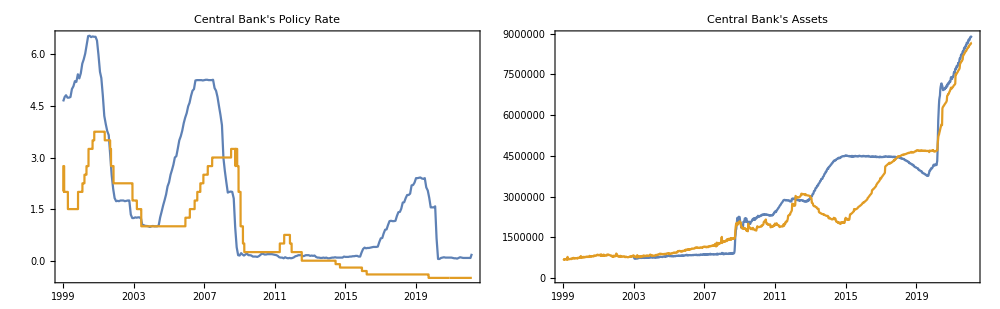

```mathematica
rate=DateListPlot[{rateUS,rateEU},PlotRange->All,PlotLabel->"Central Bank's Policy Rate",GridLines->Automatic];
assets=DateListPlot[{assetsUS,assetsEU},PlotRange->All,PlotLabel->"Central Bank's Assets",GridLines->Automatic];
GraphicsGrid[{{rate,assets}},ImageSize->1000,Spacings->0]
```

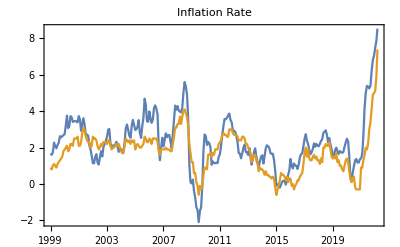

```mathematica
inflation=DateListPlot[{inflationUS,inflationEU},PlotRange->All,PlotLabel->"Inflation Rate",GridLines->Automatic]
```

## Model

### Household

Parameters

```mathematica
φ=1;
```

Utility

```mathematica
U[c_,n_]=Log[c]-n^(1+φ)/(1+φ);
```

Plot of utility

```mathematica
Plot3D[U[c,n],{c,1,10},{n,0,1},PlotLabel->"Household - Utility",AxesLabel->{"C_t","N_t","U_t"},ImageSize->Medium]
```

-Graphics3D-

Derivatives of utility

```mathematica
Uc[c_]=D[U[c,n],{c,1}];
```

```mathematica
Ucc[c_]=D[U[c,n],{c,2}];
```

```mathematica
Un[n_]=D[U[c,n],{n,1}];
```

```mathematica
Unn[c_]=D[U[c,n],{n,2}];
```

Plot of derivatives of utility

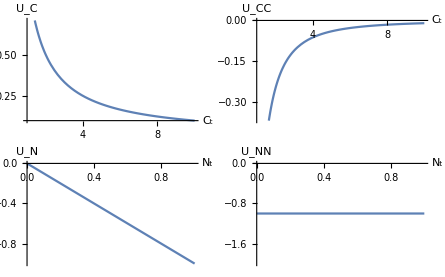

```mathematica
UcPlot=Plot[Uc[c],{c,1,10},AxesLabel->{"C_t","U_C"}];
UnPlot=Plot[Un[n],{n,0,1},AxesLabel->{"N_t","U_N"}];
UccPlot=Plot[Ucc[c],{c,1,10},AxesLabel->{"C_t","U_CC"}];
UnnPlot=Plot[Unn[n],{n,0,1},AxesLabel->{"N_t","U_NN"}];
GraphicsGrid[{{UcPlot,UccPlot},{UnPlot,UnnPlot}}]
```

## Equilibrium under Flexible Prices

### Real macroeconomic variables

Natural Aggregate Employment

```mathematica
Nn[ϵ_]:=((ϵ-1)/ϵ)^(1/(1+φ))
```

Natural Real Wage

```mathematica
WPn[ϵ_,A_]:=A*((ϵ-1)/ϵ)
```

Natural Aggregate Output

```mathematica
Yn[ϵ_,A_]:=A*((ϵ-1)/ϵ)^(1/(1+φ))
```

Natural Aggregate Real Profit

```mathematica
Dn[ϵ_,A_]:=A/ϵ*((ϵ-1)/ϵ)^(1/(1+φ))
```

Plots of real macroeconomic variables

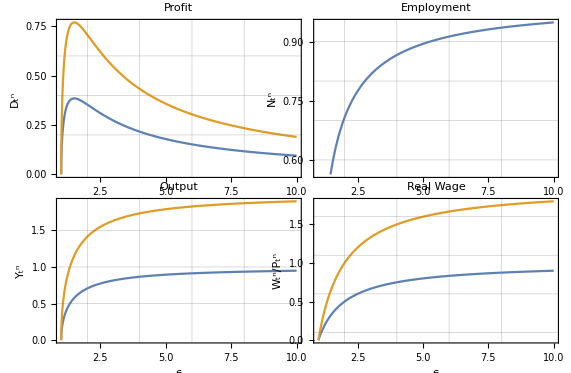

```mathematica
NnPlot=Plot[Nn[ϵ],{ϵ,1,10},PlotLabel->"Employment",FrameLabel->{"","N_t^n"},GridLines->{Range[2,9,2],Range[0.6,0.9,0.1]},Frame->True];
WPnPlot=Plot[{WPn[ϵ,1],WPn[ϵ,2]},{ϵ,1,10},PlotLabel->"Real Wage",FrameLabel->{"ϵ","W_t^n/P_t^n"},GridLines->{Range[2,9,2],Range[0.1,1.6,0.5]},Frame->True];
YnPlot=Plot[{Yn[ϵ,1],Yn[ϵ,2]},{ϵ,1,10},PlotLabel->"Output",FrameLabel->{"ϵ","Y_t^n"},GridLines->{Range[2,9,2],Range[0.5,2.0,0.5]},Frame->True];
DnPlot=Plot[{Dn[ϵ,1],Dn[ϵ,2]},{ϵ,1,10},PlotLabel->"Profit",FrameLabel->{"","D_t^n"},GridLines->{Range[2,9,2],Range[0.2,0.7,0.2]},Frame->True];
GraphicsGrid[{{DnPlot,NnPlot},{YnPlot,WPnPlot}},Spacings->{-65,-17}]
```

## Optimal Monetary Policy

### No ZLB Constraint and σ_x^2=0

Parameters

```mathematica
φ=1;
λ=2;
δ=0.3;
θ=0.5;
ϵ=6;
```

System of ODEs

```mathematica
dxdt[x_]:=(-λ*Π*(ϵ-1)/θ*(1+φ)*ⅇ^((1+φ)*x))/(1-(1+φ)*x)
dΠdt[Π_]:=Π*δ+(ϵ-1)/θ*(1-ⅇ^((1+φ)*x))
```

Phase plot of the system of ODEs

```mathematica
PhasePlot1=StreamPlot[{dxdt[x],dΠdt[Π]},{x,-0.15,0.15},{Π,-0.2,0.2},FrameLabel->{"x_t","π_t"}];
PhasePlot2=StreamPlot[{dxdt[x],dΠdt[Π]},{x,-2,2},{Π,-2,2},FrameLabel->{"x_t","π_t"}];
GraphicsGrid[{{PhasePlot1,PhasePlot2}}]
```

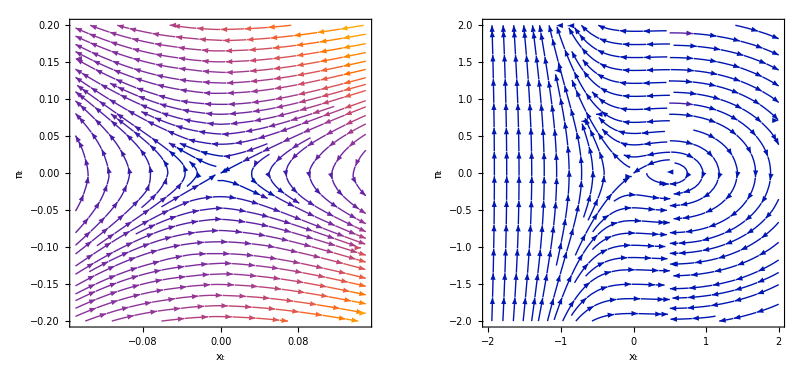

Jacobian matrix

```mathematica
J={{0,-λ*(ϵ-1)/θ*(1+φ)},{-(ϵ-1)/θ*(1+φ),δ}};
J//MatrixForm
```

(0 | -((-1+ϵ) λ (1+φ))/θ
-((-1+ϵ) (1+φ))/θ | δ)

Eigenvalues and eigenvectors

```mathematica
{e,v}=Eigensystem[J];
```

```mathematica
e//FullSimplify
```

{(δ θ-√(δ^2 θ^2+4 (-1+ϵ)^2 λ (1+φ)^2))/(2 θ),(δ θ+√(δ^2 θ^2+4 (-1+ϵ)^2 λ (1+φ)^2))/(2 θ)}

```mathematica
v//FullSimplify
```

{{(δ θ+√(δ^2 θ^2+4 (-1+ϵ)^2 λ (1+φ)^2))/(2 (-1+ϵ) (1+φ)),1},{(δ θ-√(δ^2 θ^2+4 (-1+ϵ)^2 λ (1+φ)^2))/(2 (-1+ϵ) (1+φ)),1}}

Check the eigenvalues and eigenvectors

```mathematica
J.v[[1]]==e[[1]]*v[[1]]//FullSimplify
```

True

```mathematica
J.v[[2]]==e[[2]]*v[[2]]//FullSimplify
```

True

Alternative eigenvalues and eigenvectors

```mathematica
e={(δ*θ+√(δ^2*θ^2+4*λ*(1+φ)^2*(ϵ-1)^2))/(2*θ),(δ*θ-√(δ^2*θ^2+4*λ*(1+φ)^2*(ϵ-1)^2))/(2*θ)};
```

```mathematica
v={{1,(-δ*θ-√(δ^2*θ^2+4*λ*(1+φ)^2*(ϵ-1)^2))/(2*λ*(1+φ)*(ϵ-1))},{1,(-δ*θ+√(δ^2*θ^2+4*λ*(1+φ)^2*(ϵ-1)^2))/(2*λ*(1+φ)*(ϵ-1))}};
```

Check the alternative eigenvalues and eigenvectors

```mathematica
J.v[[1]]==e[[1]]*v[[1]]//FullSimplify
```

True

```mathematica
J.v[[2]]==e[[2]]*v[[2]]//FullSimplify
```

True

Parameters

```mathematica
δ = 0.01;
μA = 0.05;
σA = 0.15;
φ = 1;
λ = 1;
θ = 2;
ϵ = 6;
```

Technology

```mathematica
SeedRandom[1];
ARandom=RandomFunction[GeometricBrownianMotionProcess[μA,σA ,1],{0,5,0.01}];
A=Normal[ARandom][[1]][[All,2]];
t={Normal[ARandom][[1]][[All,1]]};
```

Natural interest rate

```mathematica
rn=δ+μA-σA^2;
```

Natural employment

```mathematica
Nn=((ϵ-1)/ϵ)^(1/(1+φ));
```

Eigenvalue

```mathematica
Eval=(δ*θ-√(δ^2*θ^2+4*λ*(1+φ)^2*(ϵ-1)^2))/(2*θ);
```

Output gap

```mathematica
x[t_]:=0.1*ⅇ^((t-0)*Eval)
```

Inflation

```mathematica
Π[t_]:=0.02*ⅇ^((t-0)*Eval)
```

Nominal interest rate

```mathematica
i[t_]:=rn+(1-(λ*(ϵ-1)/θ*(1+φ)*ⅇ^((1+φ)*x[t]))/(1-(1+φ)*x[t]))*Π[t]
```

Aggregate employment

```mathematica
Nf[t_]:=Nn*ⅇ^x[t]
```

Aggregate output

```mathematica
Y=A*Nn*Table[ⅇ^x[t],{t,0,5,0.01}];
Y=TimeSeries[Y,t];
```

Real wage rate

```mathematica
WP=A*Table[ⅇ^((1+φ)*x[t]),{t,0,5,0.01}]*((ϵ-1)/ϵ);
WP=TimeSeries[WP,t];
```

Aggregate profit

```mathematica
Df=A*Nn*Table[ⅇ^x[t],{t,0,5,0.01}]*(1-((ϵ-1)/ϵ)*Table[ⅇ^((1+φ)*x[t]),{t,0,5,0.01}]);
Df=TimeSeries[Df,t];
```

Aggregate labor income

```mathematica
L=A*Nn*Table[ⅇ^((2+φ)*x[t]),{t,0,5,0.01}]*((ϵ-1)/ϵ);
L=TimeSeries[L,t];
```

Plots of real macroeconomic variables

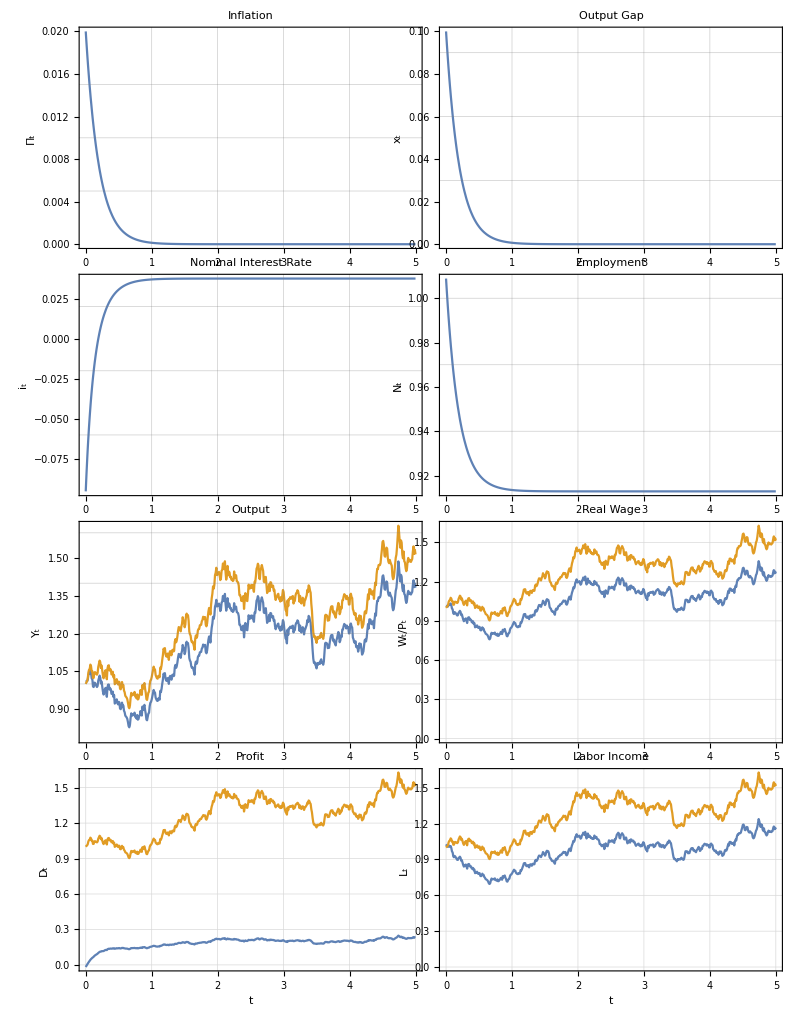

```mathematica
xPlot=Plot[x[t],{t,0,5},PlotRange->All,PlotLabel->"Output Gap",FrameLabel->{"","x_t"},GridLines->{Range[1,4,1],Range[0.03,0.09,0.03]},Frame->True];
ΠPlot=Plot[Π[t],{t,0,5},PlotRange->All,PlotLabel->"Inflation",FrameLabel->{"","Π_t"},GridLines->{Range[1,4,1],Range[0.005,0.015,0.005]},Frame->True];
iPlot=Plot[i[t],{t,0,5},PlotRange->All,PlotLabel->"Nominal Interest Rate",FrameLabel->{"","i_t"},GridLines->{Range[1,4,1],Range[-0.06,0.02,0.04]},Frame->True];
NPlot=Plot[Nf[t],{t,0,5},PlotRange->All,PlotLabel->"Employment",FrameLabel->{"","N_t"},GridLines->{Range[1,4,1],Range[0.94,1,0.03]},Frame->True];
YPlot=ListLinePlot[{Y,TimeSeries[A,t]},PlotRange->All,PlotLabel->"Output",FrameLabel->{"","Y_t"},GridLines->{Range[1,4,1],Range[1,1.6,0.2]},Frame->True];
WPPlot=ListLinePlot[{WP,TimeSeries[A,t]},PlotRange->All,PlotLabel->"Real Wage",FrameLabel->{"","W_t/P_t"},GridLines->Automatic,Frame->True];
DPlot=ListLinePlot[{Df,TimeSeries[A,t]},PlotRange->All,PlotLabel->"Profit",FrameLabel->{"t","D_t"},GridLines->Automatic,Frame->True];
LPlot=ListLinePlot[{L,TimeSeries[A,t]},PlotRange->All,PlotLabel->"Labor Income",FrameLabel->{"t","L_t"},GridLines->Automatic,Frame->True];
GraphicsGrid[{{ΠPlot,xPlot},{iPlot,NPlot},{YPlot,WPPlot},{DPlot,LPlot}},Spacings->{-65,-20}]
```